```mathematica
ClearAll["Global`*"]
```

```mathematica
v1 = {0,1};
v2 = {1.1,1.45};
V = v2 - v1;
u1 = v1;
u2 = {0.25,1.5};
U = u2 -u1;
```

```mathematica
x=U - (Dot[U,V]/Norm[V]^2) V
```

{-0.139381,0.340708}

```mathematica
Uprime = U-2x;
up1 = u1;
up2 = Uprime+up1
```

{0.528761,0.818584}

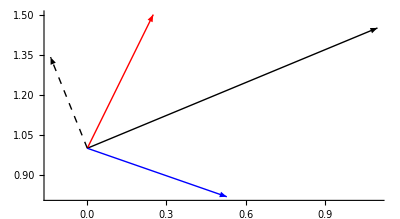

```mathematica
ph1=Graphics[{Arrow[{v1,v2}]},Axes->True];
ph2=Graphics[{Red,Arrow[{u1,u2}]},Axes->True];
ph3=Graphics[{Blue,Arrow[{up1,up2}]},Axes->True];
ph4=Graphics[{Dashed,Arrow[{up1,x+up1}]},Axes->True];
Show[ph1,ph2,ph3,ph4]
```